tamoaltas - Gráfica de un espacio ortogonal
-Graphics-

Nos dice que el campo vectorial V es ortogonal al gradiente de f en todos los puntos de la hipersuperficie Σ donde f=cte.

-Graphics-

El gradiente euclidiano es simplemente: ∇f=((∂f)/(∂x),(∂f)/(∂y))=(-2x,1)

```mathematica
(* Objeto auxiliar *)
vect:=Function[Table[#1[i],{i,1,n}]];
(* Dimension *)
n = 2;
(* Métrica *)
ηm ={{1,0},{0,1}};
Do[η[i,j] = ηm[[i,j]], {i,1,n},{j,1,n}];
```

```mathematica
(* Función y su gradiente *)
f[x_,y_]:=y-x^2;
coords[1] = x; coords[2] = y;
Do[gradf[μ]=Sum[η[μ,ν] D[f[x,y],{coords[ν]}] ,{ν,1,n}], {μ,1,n}];
vect[gradf]
```

{-2 x,1}

```mathematica
(* Grafica de f en el subespacio f(x,y) = 0 *)
curva = ContourPlot[f[x,y]==0,{x,-2,2},{y,-2,2},
ContourStyle->Directive[Red,Thick],PlotRange->All, PlotLegends->{"f(x, y) = 0"}];
```

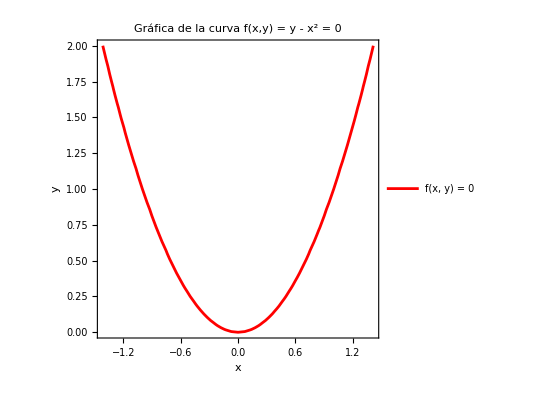

```mathematica
Show[curva,PlotLabel->"Gráfica de la curva f(x,y) = y - x^2 = 0",FrameLabel->{"x","y"}]
```

-Graphics-

Como se vio en el inciso b). La condición anterior se cumple si y solo sí el campo vectorial es ortogonal al gradiente. Un ejemplo de un vector perpendicular a uno (x,y) es el (-y,x).

```mathematica
V = {-gradf[2],gradf[1]}
```

{-1,-2 x}

-Graphics-

```mathematica
(* Dos vectores son ortogonales si su producto punto es 0 *)
Dot[vect[gradf] ,V]
```

0

```mathematica
(* Grafica del espacio vectorial V *)
espacioVectorial = VectorPlot[V,{x,-2,2},{y,-2,2},
VectorStyle->Blue,
VectorScale->{0.05,Automatic,None},
VectorPoints->15,
Epilog->{PointSize[Medium],Red,Point[{0,0}]}];
```

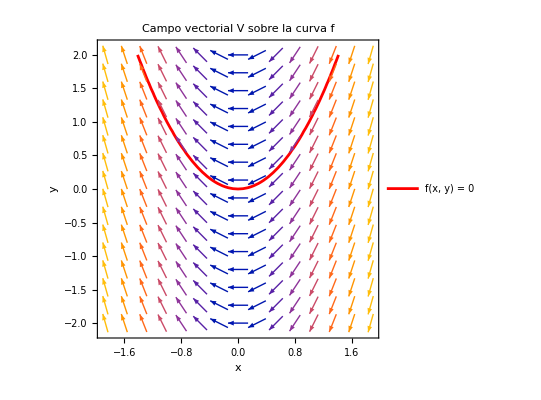

```mathematica
Show[curva,espacioVectorial ,PlotLabel->"Campo vectorial V sobre la curva f",FrameLabel->{"x","y"}
]
```